## DropPerpendicular-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Wed 7 Jun 2017 14:14:12
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

```mathematica
APoint={1,1}; 
ALineSegment={{2,4}, {3, -1}}; 
AnotherPoint={2,-1.7};
```

```mathematica
intersectionPoint=DropPerpendicular[APoint,ALineSegment]
```

{33/13,17/13}

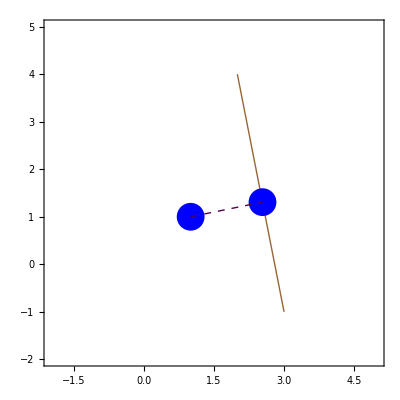

```mathematica
Show[Graphics[{
Blue, PointSize[.05], Point[APoint], 
Brown,Thick,
Line[ALineSegment],
Blue,
Point[intersectionPoint], 
Darker[Purple], Dashed, 
Line[{APoint, intersectionPoint}]}], Frame-> True, PlotRange-> {{-2,5}, {-2, 5}}, AspectRatio-> 1, Axes-> True]
```

Returns $Failed if the perpendicular from the point to the line segment does not intersect the line segment.

```mathematica
DropPerpendicular[AnotherPoint, ALineSegment]
```

$Failed

With the 3rd argument set to True, it will find as close a perpendicular as possible, by sliding the result to the nearest endpoint.

```mathematica
Nearestendpoint=DropPerpendicular[AnotherPoint, ALineSegment, True]
```

{3,-1}

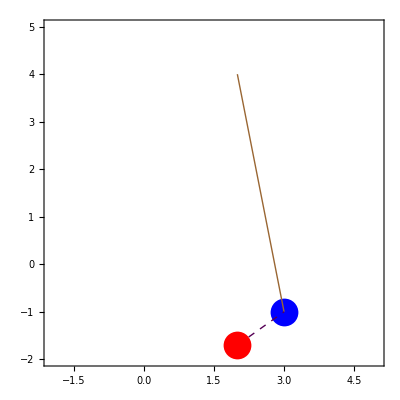

```mathematica
Show[Graphics[{
Blue, PointSize[.05], Point[Nearestendpoint], 
Brown,Thick,
Line[ALineSegment],
Darker[Purple], Dashed, 
Line[{AnotherPoint, Nearestendpoint}],
Red, Point[AnotherPoint]}], Frame-> True, PlotRange-> {{-2,5}, {-2, 5}}, AspectRatio-> 1, Axes-> True]
```